```mathematica
Quit
```

```mathematica
SetDirectory@NotebookDirectory[]
PacletDirectoryLoad["."]
<<DyonicKNGeodesics`
<<MaTeX`
```

/Users/conordyson/Documents/GitHub/Geodesics/DyonicKNGeodesics

{/Users/conordyson/Documents/GitHub/Geodesics/DyonicKNGeodesics}

$Aborted

## 2D Geodesic Plots

#### Plot Func

```mathematica
colors[i_,nmax_]:=MPLColorMap["Magma"][Log10[i (10/(1.5 nmax))]];
style[n_, thickness_:0.01]:= Table[{colors[i,n], Thickness[thickness]}, {i,1,n}];
labels[str1_, str2_] := {MaTeX[str1, Magnification->1.5], MaTeX[str2, Magnification-> 1.5]}

legend[size_,x_,y_,str1_, str2_:Automatic, str3_:Automatic, str4_:Automatic, str5_:Automatic]:=Placed[LineLegend[{MaTeX[str1, Magnification->1.1], MaTeX[str2, Magnification->1.1], MaTeX[str3, Magnification->1.1], MaTeX[str4, Magnification->1.1], MaTeX[str5, Magnification->1.1]}(*, LegendFunction->"Panel"*), LegendMarkerSize->size], {x,y}];

GeoPlungeSpacePath2D[a_,𝒪_,Ω_,δ_,ℰ_,ℒ_,𝒦_,t0_,r0_,θ0_,ϕ0_]:=Module[{orbit,t,r,θ,ϕ},
RP = 1+Sqrt[1-a^2-𝒪^2];
RM = 1-Sqrt[1-a^2-𝒪^2];
orbit = DyonicKNGeoPlunge[a,𝒪 ,Ω,δ,ℰ ,ℒ ,𝒦,{t0,r0,θ0,ϕ0}];
{t,r,θ,ϕ} = orbit["Trajectory"];
path[λ_]:=Piecewise[{
{{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]}
,r[λ]>RP},
{{None,None}
,r[λ]<=RP}
}];
path
]
style[n_, thickness_:0.01]:= Table[{colors[i,n], Thickness[thickness]}, {i,1,n}];
PlotPlungeGeos2D[a_,𝒪_,Ω_,δ_,ℰ_,ℒ_,𝒦_,t0_,r0_,θ0_,maxrec_,λmax_]:=Module[{Ppath1,Ppath2,Ppath3,Ppath4,Npath1,Npath2,Npath3,Npath4, P1,P2,P3,P4,P5,P6,P7,P8,P9 },
Ppath1[λ_] := Evaluate[GeoPlungeSpacePath2D[a,𝒪,Ω,δ,ℰ,ℒ,𝒦,0,r0,θ0,3π/2][λ]];
Ppath2[λ_] :=  Evaluate[GeoPlungeSpacePath2D[a,𝒪,Ω,δ,ℰ,ℒ,𝒦,0,r0,θ0,π/2][λ]];
Npath1[λ_] := Evaluate[GeoPlungeSpacePath2D[a,𝒪,-Ω,δ,ℰ,ℒ,𝒦,0,r0,θ0,3π/2][λ]];
Npath2[λ_] :=  Evaluate[GeoPlungeSpacePath2D[a,𝒪,-Ω,δ,ℰ,ℒ,𝒦,0,r0,θ0,π/2][λ]];
P1 = ParametricPlot[{Ppath1[λ],Npath1[λ]},{λ,0,λmax}, MaxRecursion->maxrec, PlotStyle->{Orange,Purple},PlotRange->{{-15,15},{-3,3}},Prolog->{Disk[{0,0},RP]},Frame->True,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10}(*PlotLabel->MaTeX["\\mathrm{Initially\;Equatiorial\;Charged\;Particle\;Motion}", Magnification->1.5]*),PlotLegends-> legend[8,0.625,0.5, "\\mathrm{Positive}", "\\mathrm{Negative}"],ImageSize->500];
P2 = ParametricPlot[{Ppath2[λ],Npath2[λ]},{λ,0,λmax}, MaxRecursion->maxrec, PlotStyle->{Orange,Purple},PlotRange->All];
Show[P1,P2]]
```

#### Plot

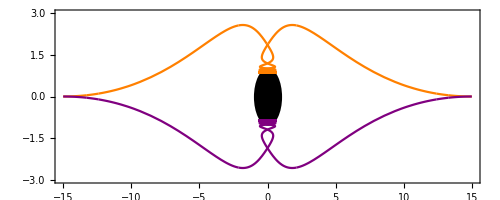

```mathematica
With[{a = 0.999,
e = 100,
Ω  = 3,
ℰ = 0.999,
ℒ = -2.6,
δ=0,
𝒦 = 0,
maxrec=10,
λmax =1},
𝒪 =Ω/e;
PlotPlungeGeos2D[a,𝒪,Ω,δ,ℰ,ℒ,𝒦,0,15,π/2,maxrec,λmax]]
```

## Energy Level-Set Plots

#### Plot Func

```mathematica
colors[i_,nmax_]:=MPLColorMap["Magma"][Log10[i (10/(1.5 nmax))]];
style[n_, thickness_:0.01]:= Table[{colors[i,n], Thickness[thickness]}, {i,1,n}];
labels[str1_, str2_] := {MaTeX[str1, Magnification->1.5], MaTeX[str2, Magnification-> 1.5]};
legend[size_,x_,y_,str1_, str2_:Automatic, str3_:Automatic, str4_:Automatic, str5_:Automatic]:=Placed[LineLegend[{MaTeX[str1, Magnification->1.1], MaTeX[str2, Magnification->1.1], MaTeX[str3, Magnification->1.1], MaTeX[str4, Magnification->1.1], MaTeX[str5, Magnification->1.1]}, LegendFunction->"Panel", LegendMarkerSize->size], {x,y}];
(*FrameStyle->BlackFrame,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12}*)
PlotField[ℒ_,a_,ϵ_,{{x1_,x2_},{z1_,z2_}}]:=Module[{p},
m=1;
M=1;
e = 100;
P = Sqrt[1-a^2-ϵ^2];
Q = 0;
Ω = e P;
δ = e Q;
RP =(M+Sqrt[M^2-a^2-P^2-Q^2]);
𝒫t[r_,θ_]:= (δ r-a Ω Cos[θ])/(m( r^2+a^2  Cos[θ]^2));
𝒫ϕ[r_,θ_]:= (Ω(a^2 +r^2 )Cos[θ]-a δ  r Sin[θ]^2)/(m (r^2+a^2 Cos[θ]^2));
Σ[r_,θ_]:= r^2 + a^2 Cos[θ]^2;
Δ[r_] :=r^2-2 M r+a^2+P^2+Q^2;
gtt[r_,θ_]  := -(Δ[r]-a^2 Sin[θ]^2)/Σ[r,θ];
gtϕ[r_,θ_]  := -(a  Sin[θ]^2)/Σ[r,θ](r^2+a^2-Δ[r]);
gϕϕ [r_,θ_] := Sin[θ]^2/Σ[r,θ]( (r^2+a^2)^2-Δ[r] a^2 Sin[θ]^2);
grr[r_,θ_]  := Σ[r,θ]/Δ[r];
gθθ[r_,θ_]  := Σ[r,θ];
ℰ[r_,θ_] := 𝒫t[r,θ]-gtϕ[r,θ]/gϕϕ[r,θ] (ℒ+𝒫ϕ[r,θ])+√((Δ[r] Sin[θ]^2)/gϕϕ[r,θ](1+(ℒ+𝒫ϕ[r,θ])^2/gϕϕ[r,θ]));
ℰopp[r_,θ_] :=- 𝒫t[r,θ]-gtϕ[r,θ]/gϕϕ[r,θ] (ℒ-𝒫ϕ[r,θ])+√((Δ[r] Sin[θ]^2)/gϕϕ[r,θ](1+(ℒ-𝒫ϕ[r,θ])^2/gϕϕ[r,θ]));
ℰnu[r_,θ_] := -gtϕ[r,θ]/gϕϕ[r,θ] (ℒ)+√((Δ[r] Sin[θ]^2)/gϕϕ[r,θ](1+(ℒ)^2/gϕϕ[r,θ]));
SSC[x_]:= ColorData["SunsetColors"][x];
p1=ContourPlot[{
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==0.0,
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==-0.5,
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==-1,
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==-1.5,
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==-2.0,
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==-2.5,
ℰ[Sqrt[x^2+z^2],ArcTan[z,x]]==-3.0}, {x,x1,x2}, {z,z1,z2},
ContourStyle->{SSC[0.4],SSC[0.5],SSC[0.6],SSC[0.7],SSC[0.8],SSC[0.9],SSC[0.95]},Frame-> True, FrameStyle->BlackFrame,BaseStyle->{FontFamily->"LM Roman 12",FontSize->12},PlotLabel-> MaTeX["\\mathcal{L} = "<>ToString[ℒ]<>",a = "<>ToString[a], Magnification->1.8] ,BaseStyle->Thickness[20],AspectRatio->(z1-z2)/(x1-x2),PlotPoints->Automatic,ImageSize->400];

SSC[x_]:= ColorData["AvocadoColors"][x];

p2=ContourPlot[{
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==0,
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==-0.5,
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==-1,
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==-1.5,
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==-2,
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==-2.5,
ℰopp[Sqrt[x^2+z^2],ArcTan[z,x]]==-3}, {x,x1,x2}, {z,z1,z2},
ContourStyle->{SSC[0.4],SSC[0.5],SSC[0.6],SSC[0.7],SSC[0.8],SSC[0.9],SSC[1]}(*, 
PlotLegends->{MaTeX["Negatively\;Particle"]}*)];

SSC[x_]:= ColorData["DeepSeaColors"][x];
p3=ContourPlot[{
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==0,
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==-0.5,
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==-1,
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==-1.5,
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==-2,
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==-2.5,
ℰnu[Sqrt[x^2+z^2],ArcTan[z,x]]==-3}, {x,x1,x2}, {z,z1,z2},
ContourStyle->{SSC[0.4],SSC[0.5],SSC[0.6],SSC[0.7],SSC[0.8],SSC[0.9],SSC[1]}];
p4=ContourPlot[{
gtt[Sqrt[x^2+z^2],ArcTan[z,x]]== 0}, {x,x1,x2}, {z,z1,z2},MaxRecursion->4,ContourStyle->Purple];
Show[p1,p2,p3,p4,Graphics[Disk[{0,0},RP]]]
];
```

#### Plot

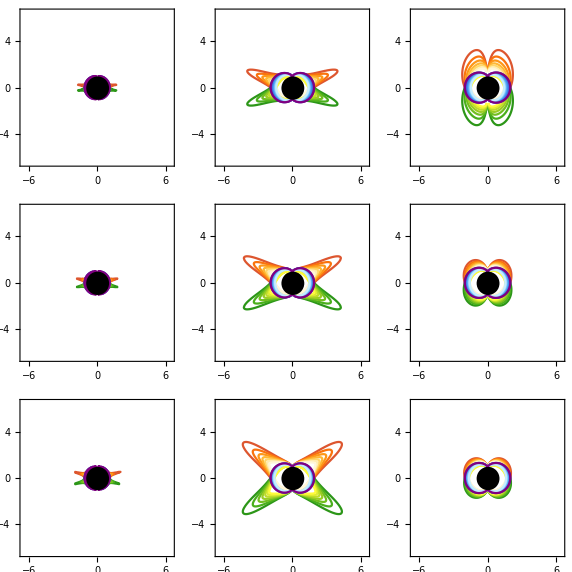

```mathematica
With[{ℒ1 = -15,ℒ2 = -20,ℒ3 =-25, a1 = 0.1, a2=0.9, a3 = 0.99},
plot BCs[ℒ_,a_]:=PlotField[ℒ,a,0.001,{{-6.5,6.5},{-6.5,6.5}}];
ℒvals = {ℒ1,ℒ2,ℒ3};
avals = {a1,a2,a3};
plots BCs = Table[plot BCs[ℒvals[[i]], avals[[j]]],{i,1,Length[ℒvals]},{j,1,Length[avals]} ];
GraphicsGrid[plots BCs,ImageSize->{Automatic, 500}]
]
```